## Preamble

```mathematica
BeginPackage["cosmomathica`",{"cosmomathica`interface`","cosmomathica`halofit`"}]
```

```mathematica
$location=DirectoryName[$InputFileName];
```

```mathematica
Cosmology::usage="This list of rules defines the background cosmology."
```

```mathematica
SetCosmology::usage="Modify the fiducial cosmology by passing the new options to this function."
```

```mathematica
Fiducial::usage="Fiducial[X] returns the fiducial value of parameter X."
```

```mathematica
Redshift::usage="Redshift[a] returns the redshift as a function of the scale factor, i.e. z=1/a-1."
```

```mathematica
Hubble::usage="Hubble[z] returns the Hubble parameter at a given redshift z."
```

```mathematica
ScaleFactor::usage="ScaleFactor[t] returns a at cosmic time t."
```

```mathematica
DimensionlessHubble::usage="DimensionlessHubble[z] returns the Hubble parameter at a given redshift z divided by the Hubble constant today."
```

```mathematica
w::usage="w[z] returns the equation of state at redshift z using the CPL parameterization."
```

```mathematica
GrowthFunction::usage="GrowthFunction[z] returns the growth function at redshift z, parameterized by the growth index."
```

```mathematica
GrowthFactor::usage="GrowthFactor[z] returns the growth factor at redshift z, parameterized by the growth index."
```

```mathematica
OmegaM::usage="OmegaM[z] returns the relative matter density at redshift z."
```

```mathematica
Distance::usage="Distance[z] accepts the Option DistanceType with the possible values Comoving, TransverseComoving, AngularDiameter, Luminosity or LookBack. Distance[z1, z2] gives the distance between two galaxies at redshifts z1 and z2 along the line of sight."
```

```mathematica
TransferFunction::usage="TransferFunction[k,path] returns a list of five values using the fitting formulae by Eisenstein&Hu(1999). The values are: The full transfer function, the baryon transfer function, the CDM transfer function, the no-wiggles transfer function, and the no-baryon transfer function. The path to the MathLink executable needs to be passed by path."
```

```mathematica
LinearPS::usage="LinearPS[k,z,path] returns a list of five values using the fitting formulae by Eisenstein&Hu(1999). The values are: The full linear power spectrum, the baryon power spectrum, the CDM power spectrum, the no-wiggles power spectrum, and the no-baryon power spectrum."
```

```mathematica
PowerSpectrum::usage="PowerSpectrum[k,z] returns the power spectrum at wavenumber k and redshift z. The algorithm can be specified with PSType."
```

```mathematica
FindSigma8Norm::usage="FindSigma8Norm[PS] returns the factor you need to multiply the power spectrum PS[k] with to have it normalized to σ_8."
```

```mathematica
NonlinearPowerSpectrumTRG::usage="NonlinearPowerSpectrumTRG[k,LinearPS,Omega21,Omega22] returns the power spectrum at wavenumber k and redshift z using the background functions Omega21 and Omega22 as specified by the TRG package. LinearPS[k] is a one-parameter function representing the linear power spectrum."
```

```mathematica
NonlinearPowerSpectrumHalofit::usage="NonlinearPowerSpectrumHalofit[k,LinearPS] returns the power spectrum at wavenumber k and redshift z using the Halofit algorithm. LinearPS[k] is a one-parameter function representing the linear power spectrum."
```

```mathematica
(*Options*)
OmegaB::usage="Baryon density"
OmegaC::usage="Cold dark matter density"
OmegaL::usage="Dark energy density"
OmegaTot::usage="Total density"
OmegaK::usage="Curvature 'density'"
h::usage="Reduced Hubble parameter"
H0::usage="Hubble parameter"
omegaM::usage="Reduced matter density"
omegaL::usage="Reduced dark energy density"
omegaB::usage="Reduced baryon density"
omegaC::usage="Reduced cold dark matter density"
omegaK::usage="Reduced curvature 'density'"
w0::usage="Equation of state today"
w1::usage="Equation of state running parameter"
gamma::usage="Growth index"
sigma8::usage="Power spectrum amplitude"
ns::usage="Spectral index"
Tcmb::usage="Temperature of the CMB"
DistanceType::usage="Distance type"
Comoving::usage="Comoving distance"
TransverseComoving::usage="Transeverse comoving distance"
AngularDiameter::usage="Angular diameter distance"
Luminosity::usage="Luminosity distance"
TransferType::usage="Type of transfer function (FitFull etc)"
FitFull::usage="Full transfer function from the Eisenstein&Hu1999 fitting function"
FitBaryon::usage="Baryon transfer function from the Eisenstein&Hu1999 fitting function"
FitCDM::usage="CDM transfer function from the Eisenstein&Hu1999 fitting function"
FitNoWiggles::usage="'No wiggle' transfer function (wiggles removed, but baryon suppression still there) from the Eisenstein&Hu1999 fitting function"
FitZeroBaryon::usage="Transfer function in Universe with no baryons from the Eisenstein&Hu1999 fitting function"
PSType::usage="Specifies the algorithm used to compute the power spectrum"
betaP::usage="betaP"
z0::usage="z0"
ShapeFactor::usage="Shape"
```

```mathematica
Cosmomathica::UnkownOption="Option `1` has an invalid value: `2`";
```

## Main

```mathematica
Begin["`Private`"]
```

### Parameters

```mathematica
zmax=100;
```

```mathematica
SetCosmology[o:OptionsPattern[]]:=Module[{clist},
clist=List[o];
(DownValues[#]={Last@DownValues[#]})&/@{odesol, antideriv1, antideriv2,transferfitint, normalization,nonlineartrgint,nonlinearhaloint};
Unprotect[Cosmology];
Do[Cosmology[[First@First@Position[Cosmology,opt[[1]],{2}]]]=opt,{opt,clist}];
Protect[Cosmology];
];
```

```mathematica
Unprotect[Cosmology];
Cosmology={OmegaM->.25,
OmegaB->.05,
OmegaC->OmegaM-OmegaB,
OmegaL->.75,
OmegaTot->OmegaM+OmegaL,
OmegaK->1-OmegaTot,
h->.7,
H0->h *1./3000,(*Units: c/Mpc*)
omegaM->OmegaM h^2,
omegaL->OmegaL h^2,
omegaB->OmegaB h^2,
omegaC->OmegaC h^2,
omegaK->OmegaK h^2,
w0->-1,
w1->0,
gamma->.545,(*growth index*)
sigma8->.8,
ns->.9,
Tcmb->2.728};
Protect[Cosmology];
cosmoopts:=Cosmology~Join~{DistanceType->"Comoving",PSType->"EH",TransferType->"full",betaP->1.5,z0->1.,ShapeFactor->.21};
```

```mathematica
OV[x_,opts:OptionsPattern[]]:=(OptionValue@x/.If[List@opts!={},List@opts,1->1]//.cosmoopts);
Options[OV]:=cosmoopts;
```

```mathematica
Fiducial[x_,opts:OptionsPattern[]]:=OV[x,opts];
Options[Fiducial]:=cosmoopts;
```

### Cosmological background functions

```mathematica
Redshift=Compile[{{a,_Real}},1/a-1];
```

```mathematica
w[z_,opts:OptionsPattern[]]:=OV[w0,opts]+OV[w1,opts]*z/(1+z);
Options[w]:=cosmoopts;
fw[z_,opts:OptionsPattern[]]=Integrate[(1+w[z,opts])/(1+zx),{zx,0,z},GenerateConditions->False];
```

```mathematica
(* H in units of H_0 *)
DimensionlessHubble[z_?NumericQ,opts:OptionsPattern[]]:=Sqrt[OV[OmegaM,opts]*(1+z)^3+OV[OmegaK,opts]*(1+z)^2+OV[OmegaL,opts]*Exp[3*fw[z,opts]]];
Options[DimensionlessHubble]:=cosmoopts;
```

```mathematica
Hubble[z_?NumericQ,opts:OptionsPattern[]]:=OV[H0,opts]DimensionlessHubble[z,opts];
Options[Hubble]:=cosmoopts;
```

```mathematica
(*TODO: Cover closed Universe; make sure a=0 at some point*)
odesol[opts:OptionsPattern[]]:=odesol[opts]=Quiet@NDSolve[{a'[t]/a[t]== Hubble[1/a[t]-1,opts],a[1]==1},a,{t,-2/Hubble[0,opts],1/Hubble[0,opts]}][[1,1,2]];
ScaleFactor[t_?NumericQ,opts:OptionsPattern[]]:=odesol[opts][t];
Options[ScaleFactor]:=cosmoopts;
Options[odesol]:=cosmoopts;
```

```mathematica
OmegaM[z_?NumericQ,opts:OptionsPattern[]]:=OV[OmegaM,opts]*(1+z)^3/DimensionlessHubble[z,opts]^2;
Options[OmegaM]:=cosmoopts;
```

```mathematica
sinn=Compile[{{x,_Real},{ok,_Real}},Evaluate@If[ok==0,x,Sinh[Sqrt[ok]x]/Sqrt[ok]]];
```

```mathematica
antideriv1[opts:OptionsPattern[]]:=antideriv1[opts]=NDSolve[{y'[zx]==1/Hubble[zx,opts],y[0]==0},y,{zx,0,zmax},MaxStepSize->.02][[1,1,2]];
antideriv2[opts:OptionsPattern[]]:=antideriv2[opts]=NDSolve[{y'[zx]==1/Hubble[zx,opts]/(1+z),y[0]==0},y,{zx,0,zmax},MaxStepSize->.02][[1,1,2]];
Distance[z_?NumericQ,opts:OptionsPattern[]]:=Switch[OptionValue@DistanceType,
"Comoving",antideriv1[opts][z],
"TransverseComoving",sinn[Distance[z,DistanceType->Comoving,opts],OV[OmegaK,opts]],
"AngularDiameter",Distance[z,DistanceType->TransverseComoving,opts]/(1+z),
"Luminosity",Distance[z,DistanceType->TransverseComoving,opts]*(1+z),
"LookBack",antideriv2[opts][z]
];
Distance[z1_?NumericQ,z2_?NumericQ,opts:OptionsPattern[]]:=Switch[OptionValue@DistanceType,
"Comoving",Distance[z2,opts]-Distance[z1,opts],
"TransverseComoving",Null,
"AngularDiameter",Null,
"Luminosity",Null,(*TODO*)
"LookBack",Distance[z2,opts]-Distance[z1,opts]];
Options[Distance]:=cosmoopts;
```

```mathematica
(*growth factor*)

GrowthFactor[z_?NumericQ,opts:OptionsPattern[]]:=OmegaM[z,opts]^OV[gamma,opts];
Options[GrowthFactor]:=cosmoopts;
antideriv3[opts:OptionsPattern[]]:=antideriv3[opts]=NDSolve[{y'[zx]==-GrowthFactor[zx,opts]/(1+zx),y[0]==0},y,{zx,0,zmax}][[1,1,2]];
Options[antideriv3]:=cosmoopts;
GrowthFunction[z_?NumericQ,opts:OptionsPattern[]]:=Exp[antideriv3[opts][z]];
Options[GrowthFunction]:=cosmoopts;
```

### Power Spectrum and other things

#### Eisenstein&Hu

```mathematica
memoizedValues[namespace_]:=Last/@Select[ReleaseHold[First/@DownValues[globalMemo,Sort->False]/.globalMemo->List],First[#]==namespace&];
isMemoized[namespace_,hash_]:=MemberQ[memoizedValues[namespace],hash];
setMemoization[namespace_,hash_,result_]:=(globalMemo[namespace,hash]=result);
getMemoization[namespace_,hash_]:=globalMemo[namespace,hash];
clearMemoization[namespace_]:=DownValues[globalMemo]=DeleteCases[DownValues[globalMemo,Sort->False],_?(First[ReleaseHold[First@#/.globalMemo->List]]==namespace&)];
```

```mathematica
Clear[TransferFunctionMem];
TransferFunction[k_,opts:OptionsPattern[]]:=Module[{oM,fB,Tc,hh,result},

hh=OV[h,opts];
oM=OV[omegaM,opts];
Tc=OV[Tcmb,opts];
fB=OV[OmegaB,opts]/OV[OmegaM,opts];

TransferFunctionMem[oM_,fB_,Tc_,hh_]:=TransferFunctionMem[oM,fB,Tc,hh]=Transfer[oM,fB,Tc,hh];
TransferFunctionMem[oM_,fB_,Tc_,hh_,type_]:=TransferFunctionMem[oM,fB,Tc,hh,type]=Interpolation[Transpose[{Transfer["kvalues"],Transfer[OV[TransferType,opts]]}/.TransferFunctionMem[oM,fB,Tc,hh]]];

TransferFunctionMem[oM,fB,Tc,hh,OV[TransferType,opts]]@(k/OV[h,opts])
]
```

```mathematica
(*linear ps*)
(*See Amendola&Tsujikawa 4.212*)
(*LinearPS[k_,z_,opts:OptionsPattern[]]:=TransferFunction[k,opts]^2 * (k/OV[H0,opts])^OV[ns,opts]* GrowthFunction[z,opts]^2/OV[H0,opts]^3*2 Pi^2*(3.2*^-10);*)

tophatFT[x_]:=3/x^3(Sin[x]-x Cos[x]);
normalization[opts:OptionsPattern[]]:=normalization[opts]=OV[sigma8,opts]/Sqrt@NIntegrate[Exp[3 lk]/(2Pi^2) (TransferFunction[Exp[lk]*OV[h,opts],opts]^2 * Exp[lk*OV[ns,opts]])tophatFT[8Exp[lk]]^2,{lk,Log[10^-6],Log[10^4]},PrecisionGoal->5];
LinearPS[k_,z_,opts:OptionsPattern[]]:=TransferFunction[k*OV[h,opts],opts]^2 * k^OV[ns,opts]* GrowthFunction[z,opts]^2*normalization[opts]^2;Options[LinearPS]:=cosmoopts;
Options[normalization]:=cosmoopts;
```

```mathematica
FindSigma8Norm[PS_,opts:OptionsPattern[]]:=OV[sigma8,opts]^2/NIntegrate[Exp[3lk]/(2Pi^2) PS[Exp[lk]]tophatFT[8Exp[lk]]^2,{lk,Log[10^-6],Log[10^4]},PrecisionGoal->5];
Options[FindSigma8Norm]:=cosmoopts;
```

#### Unification of the above

```mathematica
(*Umberella function for the power spectrum*)
Needs["Combinatorica`"];
Clear[HalofitMem,CosmicEmuMem];
PowerSpectrum[k_?NumericQ,z_?NumericQ,opts:OptionsPattern[]]:=Module[{PS,ww,hh,OM,OL,OB,gS,s8,n,bP,zz0,hfdata},

OM=OV[OmegaM,opts];
OL=OV[OmegaL,opts];
OB=OV[OmegaB,opts];
s8=OV[sigma8,opts];
n=OV[ns,opts];
hh=OV[h,opts];
ww=OV[w0,opts];

Switch[OV[PSType,opts],
"BBKS"|"PD96"|"Halofit",
bP=OptionValue[betaP];
zz0=OptionValue[z0];
gS=OptionValue[ShapeFactor];
HalofitMem[OM_,OL_,Shape_,s8_,n_,betaP_,z0_]:=HalofitMem[OM,OL,Shape,s8,n,betaP,z0]=Halofit[OM,OL,Shape,s8,n,betaP,z0];
hfdata=HalofitMem[OM,OL,gS,s8,n,bP,zz0];
HalofitMem[OM_,OL_,Shape_,s8_,n_,betaP_,z0_,type_]:=HalofitMem[OM,OL,Shape,s8,n,betaP,z0,type]=
Interpolation@Transpose[{CartesianProduct[Halofit["kvalues"]/.hfdata,Halofit["avalues"]/.hfdata],Flatten@Transpose[Halofit[OV[PSType,opts]]/.hfdata]}];
PS=HalofitMem[OM,OL,gS,s8,n,bP,zz0,OV[PSType,opts]][#1*2998(*halofit uses other units*),1/(#2+1)]*( 2998)^3&;
,

"CosmicEmu",(*TODO: extrapolation for small k*)
CosmicEmuMem[oM_,oB_,s8_,n_,w_]:=CosmicEmuMem[oM,oB,s8,n,w]=With[{cedata=CosmicEmu[oM,oB,s8,n,w]},Interpolation@Transpose[{CartesianProduct[First@(CosmicEmu["pk"]/.cedata)[[All,All,1]],CosmicEmu["zvalues"]/.cedata],Flatten@Transpose[(CosmicEmu["pk"]/.cedata)[[All,All,2]]]}]];
PS=CosmicEmuMem[OM*hh^2,OB hh^2,s8,n,ww][#1/hh,#2]*hh^3&;

,_,Message[Cosmomathica::UnkownOption,"PSType",OV[PSType,opts]];Abort[];
];

PS[k,z]
];
Options[PowerSpectrum]:=cosmoopts;
```

### Nonlinear Powerspectrum

Interpolated functions should not depend on all option parameters, or else they will be computed every time one parameter changes, even if the function doesn’t actually depend on that parameter.

#### Smith Halofit

#### TRG

```mathematica
(*Get[$location<>"psnonlinear.m"];
Needs["NumericalCalculus`"];
nonlineartrgint[LinearPS_,Omega21_,Omega22_,dlogGdz_,locH0_,locns_]:=nonlineartrgint[LinearPS,Omega21,Omega22,dlogGdz,locH0,locns]=Module[{pstable,klist,result,zz},
pstable=Transpose@Table[{k,LinearPS[k]},{k,10^Range[-4,3,.01]}];
result=Transpose@TRGPowerSpectrum[pstable,35,0,dlogGdz,locH0,locns,Omega21,Omega22];
Interpolation[result[[All,{1,2}]]]
];
NonlinearPowerSpectrumTRG[k_,LinearPS_,Omega21_,Omega22_,opts:OptionsPattern[]]:=nonlineartrgint[LinearPS,Omega21,Omega22,Abs@ND[Log[GrowthFunction[zz,opts]],zz,35],OV[H0,opts],OV[ns,opts]][k];
Options[NonlinearPowerSpectrumTRG]:=cosmoopts;*)
```

```mathematica
End[ ]
EndPackage[ ]
```

## Test

```mathematica
Get[NotebookDirectory[]<>"cosmomathica.m"]
```

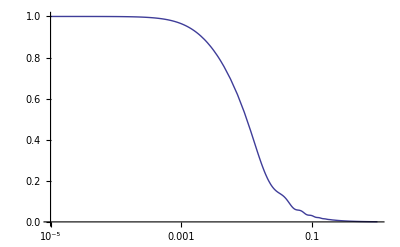

```mathematica
LogLinearPlot[TransferFunction[k,TransferType->"full",OmegaB->.08],{k,.00001,1}]
```

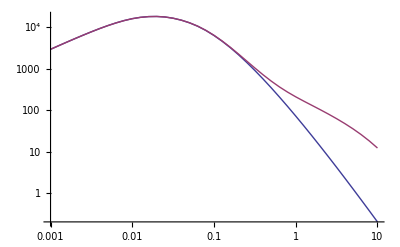

```mathematica
pstable=Table[{k,PowerSpectrum[k,0.,PSType->"BBKS",OmegaB->.045,sigma8->.85]},{k,10^Range[-3,1,.1]}];
pstablenl=HaloFitCorrection[pstable,Fiducial[OmegaM],Fiducial[OmegaL]];
ListLogLogPlot[{pstable,pstablenl},Joined->True]
```

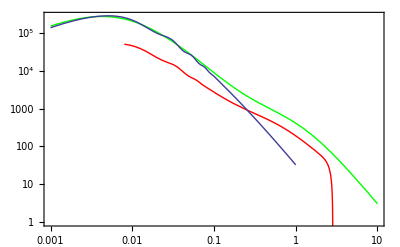

```mathematica
Show[LogLogPlot[PowerSpectrum[k,0.,PSType->"Halofit",OmegaB->.045,sigma8->.85,ShapeFactor->.05,betaP->1.5,z0->.9/1.412],{k,0.001,10},PlotStyle->Green],LogLogPlot[PowerSpectrum[k,0.,PSType->"CosmicEmu",OmegaB->.045,sigma8->.85],{k,0.008,10},PlotStyle->Red],
LogLogPlot[7.812965695782821*^7k^Fiducial[ns]TransferFunction[k,TransferType->"full",OmegaB->.045,sigma8->.85,h->.64]^2,{k,.001,1}]]
```

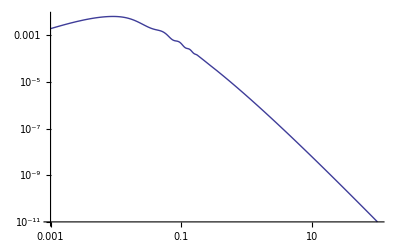

```mathematica
LogLogPlot[k^Fiducial[ns]TransferFunction[k,TransferType->"full",OmegaB->.06]^2,{k,.001,100}]
```

```mathematica
FindSigma8Norm[#^Fiducial[ns]TransferFunction[#,TransferType->"full",OmegaB->.045,sigma8->.85,h->.64]^2&,sigma8->.85]
```

7.81297×10^7